```mathematica
SetDirectory["/users/maxzweig/fuelthrust"];

propStateCostatev2[ics_, isp_, tf_, tmax_, A_] := Module[{vars, dyn},
mag[lxv_, lyv_, lzv_] :=(lxv ^ 2+ lyv ^2 + lzv ^2) // Sqrt;
switchingfunc [lxv_, lyv_, lzv_, lmag_, mas_, c_] := mag[lxv, lyv, lzv] - lmag mas /c; 
vars={x,y,z,vx,vy,vz,m,lxr,lyr,lzr,lxv,lyv,lzv,lm};
eqnsOpt = Join[(- A // Transpose).{lxr, lyr, lzr, lxv, lyv, lzv}, {(*-*)( 1/2 +Sign[switchingfunc[lxv, lyv, lzv, lm, m, isp]] / 2)tmax mag[lxv, lyv, lzv]  / (m ^2)}];
eqnsStateOpt={  2 vy n + 3n^2 x,    -2 n vx, - n^2 z  } + (1/m)( 1/2 +Sign[switchingfunc[lxv, lyv, lzv, lm, m, isp]] / 2) tmax (*(-)*){lxv, lyv, lzv} / mag[lxv, lyv, lzv];
dyn=Join[Join[{vx,vy,vz},Join[eqnsStateOpt, {- ( 1/2 +Sign[switchingfunc[lxv, lyv, lzv , lm, m, isp]] / 2)tmax/isp}]],eqnsOpt];
soln =  NDSolveValue[
Join[Thread[(#'[t]&/@vars[[1;;14]])==(dyn/.Thread[vars->(#[t]&/@vars)])],
Thread[(#[0]&/@vars)==ics]],
vars,  {t, tf, tf}, Method -> "BDF"
];
#[tf]&/@soln
]
rootfind[init_, mm_, direction_, A_, m0_, isp_, timeLength_, tm_, fm_] := Module[{},
initAngle = ArcTan[init[[1]], init[[2]]];
s = MatrixExp[-(A //Transpose) timeLength];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];
cons[dey_, lf_, xf_, mmax_] := Module[{},
udd = (2 // IdentityMatrix) - ({dey} // Transpose).{dey};
c1 ={ (udd.{xf[[1]], xf[[2]]})[[1]] } ;
c2 =  If [timeLength tm / isp<=mmax, {((m0 - xf[[7]]) -timeLength tm / isp)}, {((m0 - xf[[7]]) -mmax)}];
Join[c1, c2] // Flatten
];
falt[joint_]:= Module[{out},
out= propStateCostatev2[Join[{0,0,0,0,0,0,m0},   Join[Join[fm {joint[[1]] // Cos , joint[[1]] // Sin, 0}, ({v4, v5} /. subs ) /. {v1->(fm(joint[[1]] // Cos)), v2 ->(fm(joint[[1]] // Sin))} ], {0, joint[[2]] * ((fm {joint[[1]] // Cos, joint[[1]] // Sin}) // Norm)}]], isp, timeLength, tm, A];
cons[direction, out[[8;;14]], out[[1;;7]] , mm]
];
poss = FindRoot[falt[l], {{l, {initAngle,  init[[3]]/((fm {initAngle // Cos, initAngle // Sin})   // Norm)} }}, Evaluated->False, PrecisionGoal->20];
(** if poss does not satisfy the directional and mass constraints within satisfaction, try again with the two other possible values for lambda y, and pick the best **)
{fm (poss[[1, 2, 1]] // Cos), fm (poss[[1, 2, 1]] // Sin), poss[[1, 2, 2]] * fm}
]
```

{v4→0.+218.374 v1-1604.25 v2,v5→0.+573.594 v1+1206.15 v2}

{1200,2}

{1200,6}

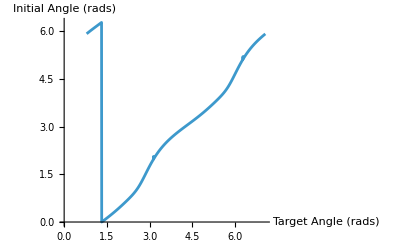

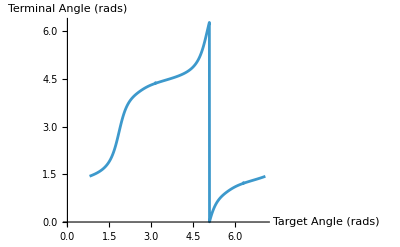

```mathematica
A = {{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1,0}, {0,0,0,0,0,1}, {3 n^2, 0, 0, 0, 2n, 0}, {0, 0, 0, -2n, 0,0}, {0, 0, -n^2, 0, 0, 0}};
mu1 = 3.986 10^14 ;
endTime = 2000;
alpha = 7780000;
n = (mu1 / alpha^3)^(1/2);
isp = 10000;
tmaxval = 0.002;
m0 = 1;
fuelpercent =0.675;

s = MatrixExp[-(A //Transpose) endTime];
subs = Solve[s[[4;;5]].{v1, v2, v3, v4, v5, v6} =={0,0}, {v1, v2, v3, v4, v5, v6}][[1]];

fuelcostates = ReadList["costatefuellim2000file"];
thrustcostates = ReadList["costatefullthrust2000file"];

subs // Print;

tcos = thrustcostates[[1,1]] ;
cosxy = tcos[[;;, 1;;2]];
cosxy // Dimensions // Print;


initialcostates = ((({#[[1]], #[[2]], 0, v4, v5, 0}  /. subs) /. {v1 -> #[[1]], v2 -> #[[2]]} ) &) /@ thrustcostates[[1,1]];
initialcostates // Dimensions // Print;

terminalcostates = (#.s &) /@initialcostates;

initcostateangles = ArcTan@@#&/@ (initialcostates[[;;, 4;;5]]);
termcostateangles = ArcTan@@#&/@ (terminalcostates[[;;, 4;;5]]);


l1 = ListLinePlot[ {thrustcostates[[1,2]] , Mod[initcostateangles, 2 Pi] } // Transpose, AxesLabel->{"Target Angle (rads)","Initial Angle (rads) "} ]
l2 = ListLinePlot[ {thrustcostates[[1,2]] , Mod[termcostateangles, 2 Pi] } // Transpose, AxesLabel->{"Target Angle (rads)","Terminal Angle (rads) "} ]
```